```mathematica
ClearAll["Global`*"];

A12=RandomReal[];
A21=RandomReal[{-.5,1}];
P=RandomReal[{200,1500}];
Aa=8.08097;
Ba=1582.271;
Ca=239.726;
Ab=8.07131;
Bb=1730.63;
Cb=233.426;

(**Vapor pressure of two components as a function of temperature (deg. C)**)
VPa=10^(Aa-Ba/(Ca+T));
VPb=10^(Ab-Bb/(Cb+T));

(**Murphree Efficiency is 100%. I left this here in case we want to add/change it in the future**)
mve=1;

(**Defines activity coefficient**)
Clear[T,i];
γ1[i_]=Exp[x2[i]^2*(A12+2*(A21-A12)*(1-x2[i]))];
γ2[i_]=Exp[(1-x2[i])^2*(A21+2*(A12-A21)*x2[i])];

(**Creates table of values defining random equilibrium curve using modified Raoult's Law**)
i=0;
While[i<101,{x2[i]=i*0.01,T[i]=FindRoot[P==VPb*γ1[i]*(1-x2[i])+VPa*γ2[i]*x2[i],{T,60},AccuracyGoal->3][[1,2]],y2[i]=x2[i]+(((VPa*γ2[i]*x2[i]/P)-x2[i])*mve)/.T->T[i],i++}];
tb=Table[{x2[i],y2[i]},{i,0,100}]

(**The consolidated "function" of the equilibrium curve generated from the table of values**)
equilb=Interpolation[tb]

(**Plots EQ curve as a line connecting the table of values**)
eqgraphic = Graphics[Line[tb]];
```

{{0.,0.},{0.01,0.0330078},{0.02,0.0653396},{0.03,0.0969486},{0.04,0.127796},{0.05,0.157849},{0.06,0.187084},{0.07,0.215481},{0.08,0.243028},{0.09,0.269719},{0.1,0.295549},{0.11,0.320522},{0.12,0.344643},{0.13,0.367921},{0.14,0.390368},{0.15,0.411999},{0.16,0.432831},{0.17,0.452882},{0.18,0.472172},{0.19,0.490722},{0.2,0.508553},{0.21,0.52569},{0.22,0.542154},{0.23,0.557968},{0.24,0.573156},{0.25,0.587741},{0.26,0.601746},{0.27,0.615194},{0.28,0.628106},{0.29,0.640505},{0.3,0.652413},{0.31,0.663849},{0.32,0.674834},{0.33,0.685387},{0.34,0.695528},{0.35,0.705275},{0.36,0.714646},{0.37,0.723657},{0.38,0.732325},{0.39,0.740665},{0.4,0.748694},{0.41,0.756425},{0.42,0.763873},{0.43,0.77105},{0.44,0.777971},{0.45,0.784646},{0.46,0.791088},{0.47,0.797308},{0.48,0.803318},{0.49,0.809127},{0.5,0.814745},{0.51,0.820182},{0.52,0.825447},{0.53,0.830549},{0.54,0.835497},{0.55,0.840298},{0.56,0.84496},{0.57,0.849491},{0.58,0.853898},{0.59,0.858188},{0.6,0.862367},{0.61,0.866443},{0.62,0.87042},{0.63,0.874306},{0.64,0.878106},{0.65,0.881826},{0.66,0.885472},{0.67,0.889048},{0.68,0.89256},{0.69,0.896013},{0.7,0.899412},{0.71,0.902762},{0.72,0.906067},{0.73,0.909333},{0.74,0.912565},{0.75,0.915766},{0.76,0.918942},{0.77,0.922096},{0.78,0.925234},{0.79,0.92836},{0.8,0.931479},{0.81,0.934595},{0.82,0.937712},{0.83,0.940836},{0.84,0.943972},{0.85,0.947123},{0.86,0.950295},{0.87,0.953493},{0.88,0.956722},{0.89,0.959987},{0.9,0.963294},{0.91,0.966648},{0.92,0.970056},{0.93,0.973522},{0.94,0.977053},{0.95,0.980657},{0.96,0.984339},{0.97,0.988106},{0.98,0.991967},{0.99,0.995929},{1.,1.}}

InterpolatingFunction[…]

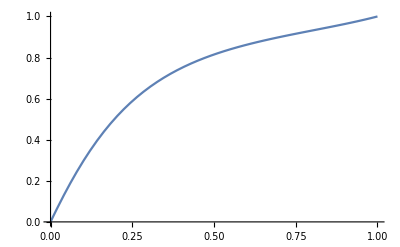

```mathematica
Plot[equilb[x],{x,0,1}]
```